-Graphics-

Reduce::naqs: {x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ is not a quantified system of equations and inequalities.

FindInstance::naqs: Reduce[{x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ] is not a quantified system of equations and inequalities.

ReplaceAll::reps: {FindInstance[Reduce[{x+Times[«2»]≤24,x+y≤9,21+Times[«2»]+Times[«2»]≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ],{x,y},ℝ]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.FindInstance[Reduce[{x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ],{x,y},ℝ]

-Graphics-

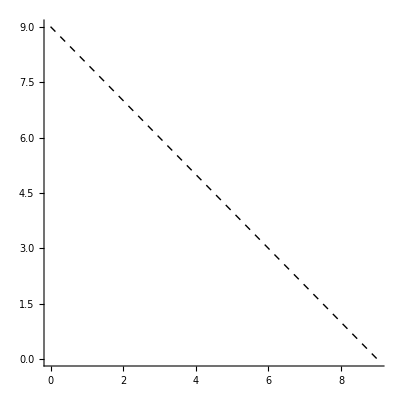

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{-3,-1},{{1,4},{1,1},{-3,-1},{-1,0},{0,-1}},{24,9,-21,0,0}]

-Graphics-

{21,{x→7,y→0}}

```mathematica
(* Задача 1: Линейно програмиране *)

(* Дефиниране на ограничителните условия *)
constraints = {
   x + 4 y ≤ 24,
   x + y ≤ 9,
   -3 x - y + 21 ≥ 0,
   x ≥ 0,
   y ≥ 0
   };

(* 1. Скициране на областта Ω *)
region = ImplicitRegion[And @@ constraints, {x, y}];
RegionPlot[region, {x, 0, 10}, {y, 0, 10},
 PlotStyle -> LightBlue,
 AxesLabel -> {"x", "y"},
 PlotLegends -> "Expressions",
 LabelStyle -> Large]

(* 2. Намиране на върховете на Ω *)
vertices = Reduce[constraints && (x | y) ∈ Reals, {x, y}, Reals];

corners = {x, y} /. FindInstance[vertices, {x, y}, Reals]

(* 3. Производствени планове и посока на нарастване на F(x, y) *)
contour = ContourPlot[3 x + y == 0, {x, 0, 10}, {y, 0, 10},
   ContourStyle -> Red, PlotRange -> All];
gradVector = Graphics[Arrow[{{0, 0}, {3, 1}}]];

Show[contour, gradVector, 
 RegionPlot[region, {x, 0, 10}, {y, 0, 10}, 
  PlotStyle -> LightBlue]]

(* 4. Анимация за оптимално решение *)
frames = Table[
   ContourPlot[3 x + y == c, {x, 0, 10}, {y, 0, 10},
    ContourStyle -> Red, PlotRange -> All], {c, 0, 30, 0.5}];
ListAnimate[frames]

(* 5. Решение с графичния метод *)
Graphics[{Dashed, Line[{{0, 9}, {9, 0}}]}, Axes -> True]

(* 6. Решение с LinearProgramming *)
objective = {3, 1}; (* Целева функция *)
matrix = {{1, 4}, {1, 1}, {-3, -1}, {-1, 0}, {0, -1}}; (* Коэффициенти *)
rhs = {24, 9, -21, 0, 0}; (* Дясна част *)
LinearProgramming[-objective, matrix, rhs]

(* 7. Всички решения *)
solution = Reduce[constraints, {x, y}, Reals];
solutionGraphics = RegionPlot[
   solution, {x, 0, 10}, {y, 0, 10}, 
   PlotStyle -> LightGreen];
Show[solutionGraphics]

(* 8. Решение с Reduce и Maximize *)
maxSolution = Maximize[{3 x + y, constraints}, {x, y}, Reals]
```

```mathematica
(* Задача 2: Линейно оптимиране *)

(* Дефиниране на ограниченията *)
constraints3D = {
   19 x - 9 y - 6 z + 20 ≥ 0,
   8 x - 10 y + 13 z - 63 ≤ 0,
   -25 x - 13 y + 11 z + 101 ≥ 0,
   -32 x + 9 y + 6 z - 7 ≤ 0,
   2 x + 26 y - 11 z + 27 ≥ 0,
   -4 x - y + 5 z + 14 ≥ 0,
   x ≥ 0,
   y ≥ 0,
   z ≥ 0
   };

(* 1. Скициране на областта Ω *)
region3D = ImplicitRegion[And @@ constraints3D, {x, y, z}];
RegionPlot3D[region3D, {x, 0, 10}, {y, 0, 10}, {z, 0, 10},
 PlotStyle -> LightBlue,
 AxesLabel -> {"x", "y", "z"},
 PlotLegends -> "Expressions"]

(* 2. Анимация за оптималните решения *)
frames3D = Table[
   ContourPlot3D[x + 2 y + z == c, {x, 0, 10}, {y, 0, 10}, {z, 0, 10},
    ContourStyle -> Opacity[0.5, Red], PlotRange -> All], {c, 0, 30, 1}];
ListAnimate[frames3D]

(* 3. Едно решение с LinearProgramming *)
objective3D = {1, 2, 1}; (* Целева функция *)
matrix3D = {{-19, 9, 6}, {8, -10, 13}, {25, 13, -11}, {32, -9, -6}, 
   {-2, -26, 11}, {4, 1, -5}, {-1, 0, 0}, {0, -1, 0}, {0, 0, -1}};
rhs3D = {-20, 63, -101, 7, -27, -14, 0, 0, 0};
LinearProgramming[-objective3D, matrix3D, rhs3D]

(* 4. Всички решения *)
solutions3D = Reduce[constraints3D, {x, y, z}, Reals];
solutionsGraphics3D = RegionPlot3D[
   solutions3D, {x, 0, 10}, {y, 0, 10}, {z, 0, 10}, 
   PlotStyle -> LightGreen];
Show[solutionsGraphics3D]
```

RegionPlot3D::boolf: ImplicitRegion[20+19 x-9 y-6 z≥0&&-63+8 x-10 y+13 z≤0&&101-25 x-13 y+11 z≥0&&-7-32 x+9 y+6 z≤0&&27+2 x+26 y-11 z≥0&&14-4 x-y+5 z≥0&&x≥0&&y≥0&&z≥0,{x,y,z}] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: ImplicitRegion[20+19 x-9 y-6 z≥0&&-63+8 x-10 y+13 z≤0&&101-25 x-13 y+11 z≥0&&-7-32 x+9 y+6 z≤0&&27+2 x+26 y-11 z≥0&&14-4 x-y+5 z≥0&&x≥0&&y≥0&&z≥0,{x,y,z}] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D[region3D,{x,0,10},{y,0,10},{z,0,10},PlotStyle→LightBlue,AxesLabel→{x,y,z},PlotLegends→Expressions]

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{-1,-2,-1},{{-19,9,6},{8,-10,13},{25,13,-11},{32,-9,-6},{-2,-26,11},{4,1,-5},{-1,0,0},{0,-1,0},{0,0,-1}},{-20,63,-101,7,-27,-14,0,0,0}]

-Graphics3D-

```mathematica
(* Задача 3: Транспортна задача *)
(* Данни за задачата *)
supply = {50, 70, 110, 90, 70};
demand = {50, 50, 100, 40, 70, 90};
costs = {
    {4, 1, 2, 4, 5, 7},
    {6, 3, 3, 5, 7, 6},
    {5, 4, 5, 8, 8, 9},
    {8, 8, 6, 6, 7, 5},
    {9, 7, 4, 5, 6, 8}
};

(* Инициализация на променливите *)
supplyLeft = supply;
demandLeft = demand;
allocation = ConstantArray[0, {Length[supply], Length[demand]}];

(* Метод на северозападния ъгъл *)
i = 1; (* започваме с първия източник *)
j = 1; (* започваме с първата дестинация *)

While[i ≤ Length[supply] && j ≤ Length[demand], 
    (* Изчисляваме минималното количество, което ще бъде транспортирано *)
    allocated = Min[supplyLeft[[i]], demandLeft[[j]]];
    allocation[[i, j]] = allocated;
    supplyLeft[[i]] -= allocated;
    demandLeft[[j]] -= allocated;
    
    (* Ако източникът е изчерпан, преминаваме към следващия *)
    If[supplyLeft[[i]] == 0, i++]; 
    (* Ако дестинацията е изчерпана, преминаваме към следващата *)
    If[demandLeft[[j]] == 0, j++];
]

(* Изчисляваме общите разходи за транспортния план *)
totalCost = Sum[allocation[[i, j]] * costs[[i, j]], {i, 1, Length[supply]}, {j, 1, Length[demand]}];

(* Показваме резултатите *)
Print["Транспортен план:"];
allocation

Print["Общи разходи:"];
totalCost

(* Задача 4: Задача за раницата *)
Knapsack[weights_, values_, capacity_] := Module[{n, dp, selectedItems, w, i},
  n = Length[weights];
  dp = Table[0, {i, 0, n}, {w, 0, capacity}];
  
  (* Запълване на таблицата за динамично програмиране *)
  For[i = 1, i ≤ n, i++,
    For[w = 0, w ≤ capacity, w++,
      If[weights[[i]] > w,
        dp[[i + 1, w + 1]] = dp[[i, w + 1]],
        dp[[i + 1, w + 1]] = Max[dp[[i, w + 1]], dp[[i, w + 1 - weights[[i]]]] + values[[i]]]
      ]
    ]
  ];

  (* Намиране на максималната стойност и събиране на избраните предмети *)
  selectedItems = {};
  w = capacity;
  For[i = n, i ≥ 1, i--,
    If[dp[[i + 1, w + 1]] ≠ dp[[i, w + 1]],
      AppendTo[selectedItems, {weights[[i]], values[[i]]}];
      w -= weights[[i]];
    ]
  ];

  (* Връщане на максималната стойност и избраните предмети *)
  {dp[[n + 1, capacity + 1]], selectedItems}
]

(* Данни *)
weights = {41, 47, 51, 6, 17, 11, 19};
values = {32, 34, 35, 8, 23, 15, 10};
capacity = 311;

(* Решение *)
{maxValue, selectedItems} = Knapsack[weights, values, capacity];
Print["Максималната стойност, която може да бъде взета е: ", maxValue];
Print["Избраните предмети са (тегло, стойност): ", selectedItems];
```

Транспортен план:

{{50,0,0,0,0,0},{0,50,20,0,0,0},{0,0,80,30,0,0},{0,0,0,10,70,10},{0,0,0,0,0,70}}

Общи разходи:

2210

Максималната стойност, която може да бъде взета е: 157

Избраните предмети са (тегло, стойност): {{19,10},{11,15},{17,23},{6,8},{51,35},{47,34},{41,32}}